```mathematica
tasks := {
    Sin[2 * x ^ 3] ^ 2 / x ^ 3,
    (x ^ 2 - 4) * Sin[(Pi * (x ^ 2)) / 6] / (x ^ 2 - 1),
    Sqrt[Abs[3 * x ^ 3 + 2 * x ^ 2 - 10 * x]] / (4 * x),
    1 / 2 * Log[Sqrt[x ^ 2 + 1] / Sqrt[x ^ 2 - 1]] - 15 * x ^ 2,
    (x ^ 3 - x ^ 2 - x + 1) ^ (1 / 3) / Tan[x],
    2 * Log[(x - 1) / x] + 1,
    Log[x - 1] / (x - 1) ^ 2
}

getVariantForNumber[number_, variationsQuo_]:=(
    Module[{t},
        t = Mod[number , variationsQuo];
        If[t ≠ 0
                , t
                , variationsQuo
            ]
    ])

yourNumber := 20
numberOfYourTask := getVariantForNumber[yourNumber, Length[tasks]]
y[t_] := tasks[[numberOfYourTask]] /. x -> t
y[x]//TraditionalForm

g := 1 - 1/x;
rootsNull :=Reduce[g > 0, x]
rootsNull
```

2 log((x-1)/x)+1

x<0||x>1

```mathematica
Plot[y[x], {x, -10, 10}, Exclusions -> rootsNull, AspectRatio -> Auto]
```

-Graphics-

```mathematica
v := y[x] - y[-x]
Print["y(x) - y(-x) = ", v]
```

y(x) - y(-x) = -2 Log[-(-1-x)/x]+2 Log[(-1+x)/x]

```mathematica
Print["T = ", FunctionPeriod[y[x], x]]
```

T = 0

```mathematica
roots := Reduce[y[x] == 0, x]
roots
```

x==(√ⅇ)/(-1+√ⅇ)

```mathematica
Print["y(0) = ", y[0]]
```

Power::infy: Infinite expression 1/0 encountered.

y(0) = ∞

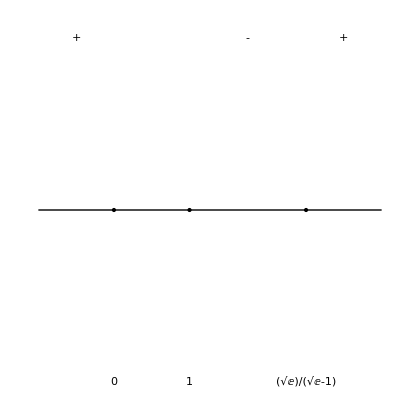

```mathematica
x1 := 0
x2 := 1
x3 := (√ⅇ)/(-1+√ⅇ)
margin := 0.2

Show[
    Graphics[Line[{{x1 - 1, 0}, {x3 + 1, 0}}]],
  Graphics[Point[{x1, 0}, VertexColors->Red]],
    Graphics[Text["0", {x1, -margin}]],
    Graphics[Point[{x2, 0}, VertexColors->Red]],
    Graphics[Text["1", {x2, -margin}]],
    Graphics[Point[{x3, 0}, VertexColors->Red]],
    Graphics[Text[Sqrt[E]/(Sqrt[E] - 1), {x3, -margin}]],
  Graphics[Text["+", {( x1 - 1) / 2, margin}]],
    Graphics[Text["-", {(x2 + x3) / 2, margin}]],
    Graphics[Text["+", {(x3 + x3 + 1) / 2, margin}]]
]
```

```mathematica
dy := D[y[x], x]
dy ==0
```

(2 (-(-1+x)/x^2+1/x) x)/(-1+x)==0

{}

```mathematica
Plot[dy /. x -> z, {z, -10, 10}]
```

-Graphics-

```mathematica
Print["lim [x -> +Infinity] y(x) = ", Limit[y[x], x -> +Infinity]]
Print["lim [x -> -Infinity] y(x) = ", Limit[y[x], x -> -Infinity]]
```

lim [x -> +Infinity] y(x) = 1

lim [x -> -Infinity] y(x) = 1

```mathematica
Show[
    Plot[y[x], {x, -20, 20}, AspectRatio ->0.7],
    Graphics[{Dashing[{.05}], Line[{{-20, 1}, {20, 1}}]}],
    Graphics[{Dashing[{.05}], Line[{{1, -20}, {1, 20}}]}],
  Graphics[{Dashing[{.05}], Line[{{-0.1, -20}, {-0.1, 20}}]}]
]
```

-Graphics-